```mathematica
SetDirectory[NotebookDirectory[]];
```

## Plot templates

```mathematica
ListLogLogPlotTemplate[Data_,Legend_,title_,xlabel_,ylabel_]:=Block[{},
ListLogLogPlot[Data,GridLines->Automatic, GridLinesStyle->Directive[Gray, Dashed],PlotLabel->title,PlotStyle->ColorData[81,"ColorList"], Frame->True,Joined->True,PlotMarkers->Automatic,FrameLabel->{xlabel,ylabel},PlotLegends->LineLegend[Legend,LegendFunction->(Framed[#,RoundingRadius->2.75]&),LegendMargins->1],LabelStyle->Directive[Black,FontSize->14,Frame->True]]
];
ListPlotTemplate[Data_,Legend_,title_,xlabel_,ylabel_]:=Block[{},
ListPlot[Data,GridLines->Automatic, GridLinesStyle->Directive[Gray, Dashed],PlotLabel->title,PlotStyle->ColorData[81,"ColorList"], Frame->True,Joined->True,PlotMarkers->Automatic,FrameLabel->{xlabel,ylabel},PlotLegends->LineLegend[Legend,LegendFunction->(Framed[#,RoundingRadius->2.75]&),LegendMargins->1],LabelStyle->Directive[Black,FontSize->14,Frame->True]]
];
```

## Timing extractor

```mathematica
ClearAll;
GetTimingData[test_,order_]:=Block[{K,R},
If[order==1,nmesh=5,nmesh=4];
K=Table[0,{nmesh},{5}];
R=Table[0,{nmesh},{5}];
For[imesh=1,imesh≤nmesh,imesh++,
	For[iout=1,iout≤5,iout++,
		filename=StringJoin[test,"/order",ToString[order],"-mesh",ToString[imesh],"/out-",ToString[iout],".txt"];
		file=Import[filename,{"Data"}];
		filelines=Dimensions[file][[1]];

		Clear[match];
		match={};
		If[test=="PZ_NOT_MODIFIED",
			stringToMatch="Calling AssembleResidual: Elasped time [sec] = ";
			For[iline=1,iline≤filelines,iline++,
				If[StringContainsQ[ToString[file[[iline]]],stringToMatch],AppendTo[match,iline],Continue];
			];
			posR = match[[1]];
			R[[imesh,iout]]=ToExpression[StringTake[file[[posR]],{StringLength[stringToMatch]+1,StringLength[stringToMatch]+6}]];
		,
			stringToMatch="K Assemble: Elasped time [sec] = ";
			For[iline=1,iline≤filelines,iline++,
				If[StringContainsQ[ToString[file[[iline]]],stringToMatch],AppendTo[match,iline],Continue];
			];
			posK = match[[2]];
			posR = match[[2]]+1;											    K[[imesh,iout]]=ToExpression[StringTake[file[[posK]],{StringLength[stringToMatch]+1,StringLength[stringToMatch]+6}]];
			R[[imesh,iout]]=ToExpression[StringTake[file[[posR]],{StringLength[stringToMatch]+1,StringLength[stringToMatch]+6}]];
		];

	];
];
If[test=="PZ_NOT_MODIFIED",Return[R],Return[{K,R}]];
];
```

## CPU K and R timing

```mathematica
type="CPU_NOT_MODIFIED";
Kcpu=Table[0.,3,5];
Rcpu=Table[0.,3,5];
{Kcpu[[1]],Rcpu[[1]]}=GetTimingData[type,1];
{Kcpu[[2]],Rcpu[[2]]}=GetTimingData[type,2];
{Kcpu[[3]],Rcpu[[3]]}=GetTimingData[type,3];
```

## GPU K and R timing

```mathematica
type="GPU_NOT_MODIFIED";
Kgpu=Table[0.,3,5];
Rgpu=Table[0.,3,5];
{Kgpu[[1]],Rgpu[[1]]}=GetTimingData[type,1];
{Kgpu[[2]],Rgpu[[2]]}=GetTimingData[type,2];
{Kgpu[[3]],Rgpu[[3]]}=GetTimingData[type,3];
```

## PZ R timing

```mathematica
type="PZ_NOT_MODIFIED";
Rpz=Table[0.,3,5];
Rpz[[1]]=GetTimingData[type,1];
Rpz[[2]]=GetTimingData[type,2];
Rpz[[3]]=GetTimingData[type,3];
```

## Mean timing

```mathematica
Kcpu1=Flatten[{Mean[Kcpu[[1,1]]],Mean[Kcpu[[1,2]]],Mean[Kcpu[[1,3]]],Mean[Kcpu[[1,4]]],Mean[Kcpu[[1,5]]]}];
Kcpu2=Flatten[{Mean[Kcpu[[2,1]]],Mean[Kcpu[[2,2]]],Mean[Kcpu[[2,3]]],Mean[Kcpu[[2,4]]]}];
Kcpu3=Flatten[{Mean[Kcpu[[3,1]]],Mean[Kcpu[[3,2]]],Mean[Kcpu[[3,3]]],Mean[Kcpu[[3,4]]]}];

Rcpu1=Flatten[{Mean[Rcpu[[1,1]]],Mean[Rcpu[[1,2]]],Mean[Rcpu[[1,3]]],Mean[Rcpu[[1,4]]],Mean[Rcpu[[1,5]]]}];
Rcpu2=Flatten[{Mean[Rcpu[[2,1]]],Mean[Rcpu[[2,2]]],Mean[Rcpu[[2,3]]],Mean[Rcpu[[2,4]]]}];
Rcpu3=Flatten[{Mean[Rcpu[[3,1]]],Mean[Rcpu[[3,2]]],Mean[Rcpu[[3,3]]],Mean[Rcpu[[3,4]]]}];
```

```mathematica
Kgpu1=Flatten[{Mean[Kgpu[[1,1]]],Mean[Kgpu[[1,2]]],Mean[Kgpu[[1,3]]],Mean[Kgpu[[1,4]]],Mean[Kgpu[[1,5]]]}];
Kgpu2=Flatten[{Mean[Kgpu[[2,1]]],Mean[Kgpu[[2,2]]],Mean[Kgpu[[2,3]]],Mean[Kgpu[[2,4]]]}];
Kgpu3=Flatten[{Mean[Kgpu[[3,1]]],Mean[Kgpu[[3,2]]],Mean[Kgpu[[3,3]]],Mean[Kgpu[[3,4]]]}];

Rgpu1=Flatten[{Mean[Rgpu[[1,1]]],Mean[Rgpu[[1,2]]],Mean[Rgpu[[1,3]]],Mean[Rgpu[[1,4]]],Mean[Rgpu[[1,5]]]}];
Rgpu2=Flatten[{Mean[Rgpu[[2,1]]],Mean[Rgpu[[2,2]]],Mean[Rgpu[[2,3]]],Mean[Rgpu[[2,4]]]}];
Rgpu3=Flatten[{Mean[Rgpu[[3,1]]],Mean[Rgpu[[3,2]]],Mean[Rgpu[[3,3]]],Mean[Rgpu[[3,4]]]}];
```

```mathematica
Rpz1=Flatten[{Mean[Rpz[[1,1]]],Mean[Rpz[[1,2]]],Mean[Rpz[[1,3]]],Mean[Rpz[[1,4]]],Mean[Rpz[[1,5]]]}];
Rpz2=Flatten[{Mean[Rpz[[2,1]]],Mean[Rpz[[2,2]]],Mean[Rpz[[2,3]]],Mean[Rpz[[2,4]]]}];
Rpz3=Flatten[{Mean[Rpz[[3,1]]],Mean[Rpz[[3,2]]],Mean[Rpz[[3,3]]],Mean[Rpz[[3,4]]]}];
```

## Timing plots

```mathematica
ndof1={7936,32256,130048,522240,2093056};
ndof2={31248,128016,518160,2084880};
ndof3={69936,287280,1164336,4687920};
```

```mathematica
RCPU1=Thread[{ndof1,Rcpu1}];
RCPU2=Thread[{ndof2,Rcpu2}];
RCPU3=Thread[{ndof3,Rcpu3}];

RGPU1=Thread[{ndof1,Rgpu1}];
RGPU2=Thread[{ndof2,Rgpu2}];
RGPU3=Thread[{ndof3,Rgpu3}];

RPZ1=Thread[{ndof1,Rpz1}];
RPZ2=Thread[{ndof2,Rpz2}];
RPZ3=Thread[{ndof3,Rpz3}];
```

```mathematica
KCPU1=Thread[{ndof1,Kcpu1}];
KCPU2=Thread[{ndof2,Kcpu2}];
KCPU3=Thread[{ndof3,Kcpu3}];

KGPU1=Thread[{ndof1,Kgpu1}];
KGPU2=Thread[{ndof2,Kgpu2}];
KGPU3=Thread[{ndof3,Kgpu3}];
```

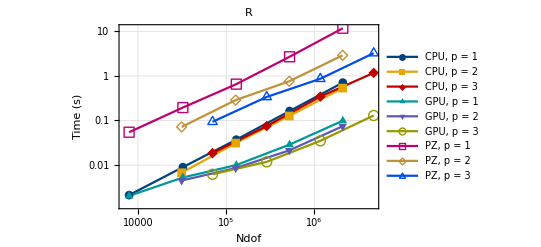

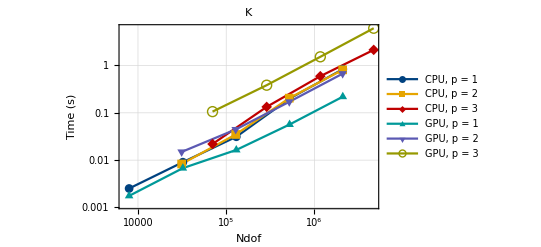

```mathematica
DataR={RCPU1,RCPU2,RCPU3,RGPU1,RGPU2,RGPU3,RPZ1,RPZ2,RPZ3};
DataK={KCPU1,KCPU2,KCPU3,KGPU1,KGPU2,KGPU3};
Legend={"CPU, p = 1","CPU, p = 2","CPU, p = 3","GPU, p = 1","GPU, p = 2","GPU, p = 3","PZ, p = 1","PZ, p = 2","PZ, p = 3"};
ListLogLogPlotTemplate[DataR,Legend,"R","Ndof","Time (s)"]
ListLogLogPlotTemplate[DataK,Legend,"K","Ndof","Time (s)"]
```

## Residual value extractor

```mathematica
GetResidualData[test_,order_]:=Block[{},
filename=StringJoin[test,"/order",ToString[order],"-mesh3/out-1.txt"];
file=Import[filename,{"Data"}];
filelines=Dimensions[file][[1]];

Rval={};
For[iline=1,iline≤filelines,iline++,	
	stringToMatch="Nonlinear process : residue norm = ";
	If[StringContainsQ[ToString[file[[iline]]],stringToMatch],
		lastpos= Flatten[TextPosition[file[[iline]],"Sentence"]][[2]];
		val=StringTake[file[[iline]],{StringLength[stringToMatch]+1,lastpos}];
		 AppendTo[Rval,val];
       ,
		Continue;
      ];
	stringToMatch="Number of iterations = ";
	If[StringContainsQ[ToString[file[[iline]]],stringToMatch],
		lastpos= Flatten[TextPosition[file[[iline]],"Sentence"]][[2]];
		 nit=ToExpression[StringTake[file[[iline]],{StringLength[stringToMatch]+1,lastpos}]];
      ,
		Continue;
      ];
];
Return[{nit,Flatten[Rval]}];
];
ConvertToNumber[form1_]:=Block[{length}, (*needed to convert scientific value in string format to number. the only way i could make it work*)
length=Length[form1];
Val={};
For[i=1,i≤length,i++,
a=Read[StringToStream[#],Number]&/@{form1[[i]]};
AppendTo[Val,a];
];
Return[Val];
];
```

## Residual values for n iterations

```mathematica
type="GPU_NOT_MODIFIED"; (*MESH = 3 / OUT = 1*)
{n1,r1}=GetResidualData[type,1];
{n2,r2}=GetResidualData[type,2];
{n3,r3}=GetResidualData[type,3];
Rval1=Flatten[ConvertToNumber[r1]];
Rval2=Flatten[ConvertToNumber[r2]];
Rval3=Flatten[ConvertToNumber[r3]];
```

```mathematica
type="GPU_MODIFIED"; (*MESH = 3 / OUT = 1*)
{nmod1,rmod1}=GetResidualData[type,1];
{nmod2,rmod2}=GetResidualData[type,2];
{nmod3,rmod3}=GetResidualData[type,3];
Rvalmod1=Flatten[ConvertToNumber[rmod1]];
Rvalmod2=Flatten[ConvertToNumber[rmod2]];
Rvalmod3=Flatten[ConvertToNumber[rmod3]];
```

## Plotting

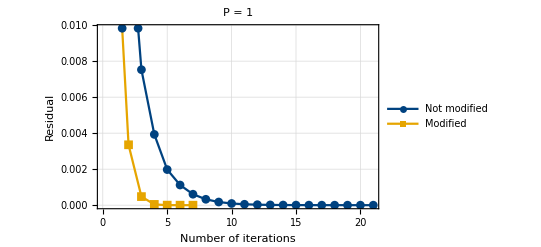

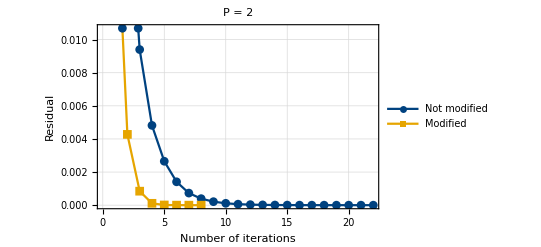

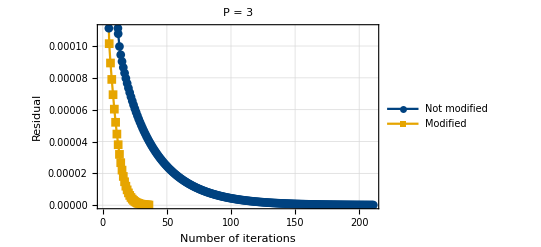

```mathematica
Legend={"Not modified","Modified"};
ListPlotTemplate[{Rval1,Rvalmod1},Legend,"P = 1","Number of iterations","Residual"]
ListPlotTemplate[{Rval2,Rvalmod2},Legend,"P = 2","Number of iterations","Residual"]
ListPlotTemplate[{Rval3,Rvalmod3},Legend,"P = 3","Number of iterations","Residual"]
```